```mathematica
Practical-2
Harshit Sahu |
BSc(Hons) Computer Science|202114114


Plotting of second order solution family of differential
equation

Question 1:Solve Second order Differential Equation y''+y=0
Solution:
```

```mathematica
DSolve[y''[x]+y[x]==0,y[x],x]
```

```mathematica
{{y[x]->C[1] Cos[x]+C[2] Sin[x]}}


Question 2:Solve Second order Differential Equation y''+y'-6y=0
Solution:
```

```mathematica
DSolve[y''[x]+y'[x]-6y[x]==0,y[x],x]
```

```mathematica
{{y[x]->ⅇ^(-3 x) C[1]+ⅇ^(2 x) C[2]}}

Question 3:Solve Second order Differential Equation 4y''+12y'-6y=0
Solution:
```

```mathematica
DSolve[4y''[x]+12y'[x]-6y[x]==0,y[x],x]
```

```mathematica
{{y[x]->ⅇ^((-3/2-(√15)/2) x) C[1]+ⅇ^((-3/2+(√15)/2) x) C[2]}}

Question 4:Solve Second order Differential Equation y''-6y'+13y=0
Solution:
```

```mathematica
DSolve[y''[x]-6y'[x]+13y[x]==0,y[x],x]
```

```mathematica
{{y[x]->ⅇ^(3 x) C[2] Cos[2 x]+ⅇ^(3 x) C[1] Sin[2 x]}}

Question 5:Solve Second order Differential Equation y''-2y'+y=0
Solution:
```

```mathematica
DSolve[y''[x]-2y'[x]+y[x]==0,y[x],x]
```

```mathematica
{{y[x]->ⅇ^x C[1]+ⅇ^x x C[2]}}


Plotting Of Solution Of Second order Differential Equations

Question 1:Solve Second order Differential Equation y''+y=0 and Plot its three Solutions.
Solution:
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]}}

Cos[x]+2 Sin[x]

Cos[x]/2+5 Sin[x]

-Cos[x]/2-4 Sin[x]

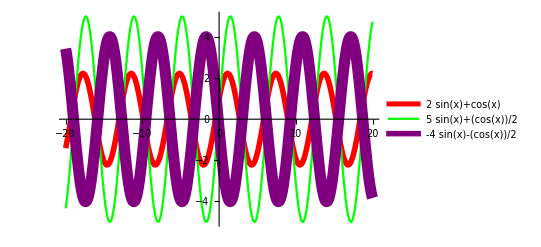

```mathematica
Sol=DSolve[y''[x]+y[x]==0,y[x],x]
Sol1=y[x]/.Sol[[1]]/.{C[1]->1,C[2]->2}
Sol2=y[x]/.Sol[[1]]/.{C[1]->1/2,C[2]->5}
Sol3=y[x]/.Sol[[1]]/.{C[1]->-1/2,C[2]->-4}
Plot[{Sol1,Sol2,Sol3},{x,-20,20},
PlotStyle->{{Red, Thickness[0.01]},{Green,Thick},{Purple,Thickness[0.02]}},
PlotLegends->{Sol1,Sol2,Sol3}]
```

```mathematica
Question 2:Solve Second order Differential Equation y''+y'-6y=0 and Plot its three Solutions.
Solution:
```

{{y[x]→ⅇ^(-3 x) C[1]+ⅇ^(2 x) C[2]}}

2.5 ⅇ^(2 x)

ⅇ^(-3 x)+5 ⅇ^(2 x)

-1/2 ⅇ^(-3 x)+5 ⅇ^(2 x)

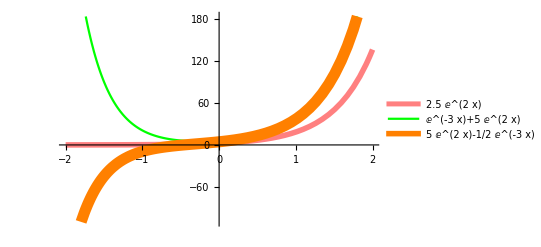

```mathematica
Sol=DSolve[y''[x]+y'[x]-6y[x]==0,y[x],x]
Sol1=y[x]/.Sol[[1]]/.{C[1]->0,C[2]->2.5}
Sol2=y[x]/.Sol[[1]]/.{C[1]->1,C[2]->5}
Sol3=y[x]/.Sol[[1]]/.{C[1]->-1/2,C[2]->5}
Plot[{Sol1,Sol2,Sol3},{x,-2,2},
PlotStyle->{{Pink, Thickness[0.01]},{Green,Thick},{Orange,Thickness[0.02]}},
PlotLegends->{Sol1,Sol2,Sol3}]
```

```mathematica
Question 3:Solve Second order Differential Equation 4y''+12y'+9y=0 and Plot its four Solutions for
(i) C[1]=-1,C[2]=4
(ii) C[1]=-3,C[2]=6
(iii) C[1]=-10,C[2]=7
(iv) C[1]=-1.5,C[2]=-5
Solution:
```

{{y[x]→ⅇ^(-3 x/2) C[1]+ⅇ^(-3 x/2) x C[2]}}

ⅇ^(-3 x/2)+4 ⅇ^(-3 x/2) x

3 ⅇ^(-3 x/2)+6 ⅇ^(-3 x/2) x

-10 ⅇ^(-3 x/2)+7 ⅇ^(-3 x/2) x

-1.5 ⅇ^(-3 x/2)-5 ⅇ^(-3 x/2) x

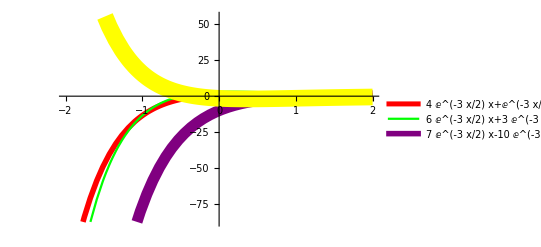

```mathematica
Sol=DSolve[4y''[x]+12y'[x]+9y[x]==0,y[x],x]
Sol1=y[x]/.Sol[[1]]/.{C[1]->1,C[2]->4}
Sol2=y[x]/.Sol[[1]]/.{C[1]->3,C[2]->6}
Sol3=y[x]/.Sol[[1]]/.{C[1]->-10,C[2]->7}
Sol4=y[x]/.Sol[[1]]/.{C[1]->-1.5,C[2]->-5}
Plot[{Sol1,Sol2,Sol3,Sol4},{x,-2,2},
PlotStyle->{{Red, Thickness[0.01]},{Green,Thick},{Purple,Thickness[0.02]},{Yellow,Thickness[0.03]}},
PlotLegends->{Sol1,Sol2,Sol3}]
```